```mathematica
- ((η-1)*Bm/Em)/(Log[1-(M*(B0/Bm)^(1/(η-1)))^(1-η)]-Log[1 - (M*(1-f0*M^(γ-1))*(B0/Bm)^(1/(η-1)))^(1-η)])/.{
η->3/4,
γ->1.19,
f0->0.0202,
B0->1.9*10^(-2),
Bm->0.0245,
Em->1
}
```

0.006125/(Log[1-1.28947 M^(1/4)]-Log[1-1.28947 ((1-0.0202 M^0.19) M)^(1/4)])

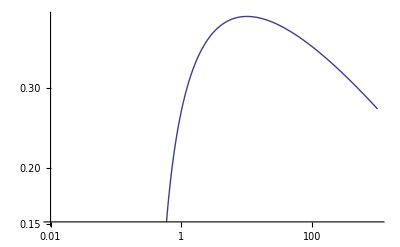

```mathematica
LogLogPlot[0.006125/(Log[1-1.2894736842105263 M^(1/4)]-Log[1-1.2894736842105263 ((1-0.0202 M^0.18999999999999995) M)^(1/4)]),{M,.01,1000}]
```

```mathematica
D[((η-1)*Bm/Em)/(Log[1-(M*(B0/Bm)^(1/(η-1)))^(1-η)]-Log[1 - (M*(1-f0*M^(γ-1))*(B0/Bm)^(1/(η-1)))^(1-η)]),M]
```

-(Bm (-((B0/Bm)^(1/(-1+η)) ((B0/Bm)^(1/(-1+η)) M)^-η (1-η))/(1-((B0/Bm)^(1/(-1+η)) M)^(1-η))+(((B0/Bm)^(1/(-1+η)) M (1-f0 M^(-1+γ)))^-η ((B0/Bm)^(1/(-1+η)) (1-f0 M^(-1+γ))-(B0/Bm)^(1/(-1+η)) f0 M^(-1+γ) (-1+γ)) (1-η))/(1-((B0/Bm)^(1/(-1+η)) M (1-f0 M^(-1+γ)))^(1-η))) (-1+η))/(Em (Log[1-((B0/Bm)^(1/(-1+η)) M)^(1-η)]-Log[1-((B0/Bm)^(1/(-1+η)) M (1-f0 M^(-1+γ)))^(1-η)])^2)

```mathematica
FullSimplify[-(Bm (-((B0/Bm)^(1/(-1+η)) ((B0/Bm)^(1/(-1+η)) M)^-η (1-η))/(1-((B0/Bm)^(1/(-1+η)) M)^(1-η))+(((B0/Bm)^(1/(-1+η)) M (1-f0 M^(-1+γ)))^-η ((B0/Bm)^(1/(-1+η)) (1-f0 M^(-1+γ))-(B0/Bm)^(1/(-1+η)) f0 M^(-1+γ) (-1+γ)) (1-η))/(1-((B0/Bm)^(1/(-1+η)) M (1-f0 M^(-1+γ)))^(1-η))) (-1+η))/(Em (Log[1-((B0/Bm)^(1/(-1+η)) M)^(1-η)]-Log[1-((B0/Bm)^(1/(-1+η)) M (1-f0 M^(-1+γ)))^(1-η)])^2)]
```

-(Bm ((-1+η)/(-M+(B0/Bm)^(1/(1-η)) ((B0/Bm)^(1/(-1+η)) M)^η)+((M-f0 M^γ γ) (-1+η))/(M (M-f0 M^γ-(B0/Bm)^(1/(1-η)) ((B0/Bm)^(1/(-1+η)) (M-f0 M^γ))^η))) (-1+η))/(Em (Log[1-((B0/Bm)^(1/(-1+η)) M)^(1-η)]-Log[1-((B0/Bm)^(1/(-1+η)) (M-f0 M^γ))^(1-η)])^2)

```mathematica
Reduce[(-1+η)/(-M+(B0/Bm)^(1/(1-η)) ((B0/Bm)^(1/(-1+η)) M)^η)==((M-f0 M^γ γ) (-1+η))/(M (M-f0 M^γ-(B0/Bm)^(1/(1-η)) ((B0/Bm)^(1/(-1+η)) (M-f0 M^γ))^η)),M]
```

$Aborted

```mathematica
FullSimplify[((-1+η)/(-M+(B0/Bm)^(1/(1-η)) ((B0/Bm)^(1/(-1+η)) M)^η))/(((M-f0 M^γ γ) (-1+η))/(M (M-f0 M^γ-(B0/Bm)^(1/(1-η)) ((B0/Bm)^(1/(-1+η)) (M-f0 M^γ))^η)))]
```

(M (M-f0 M^γ-(B0/Bm)^(1/(1-η)) ((B0/Bm)^(1/(-1+η)) (M-f0 M^γ))^η))/((-M+(B0/Bm)^(1/(1-η)) ((B0/Bm)^(1/(-1+η)) M)^η) (M-f0 M^γ γ))

```mathematica
Reduce[-(Bm (-((B0/Bm)^(1/(-1+η)) ((B0/Bm)^(1/(-1+η)) M)^-η (1-η))/(1-((B0/Bm)^(1/(-1+η)) M)^(1-η))+(((B0/Bm)^(1/(-1+η)) M (1-f0 M^(-1+γ)))^-η ((B0/Bm)^(1/(-1+η)) (1-f0 M^(-1+γ))-(B0/Bm)^(1/(-1+η)) f0 M^(-1+γ) (-1+γ)) (1-η))/(1-((B0/Bm)^(1/(-1+η)) M (1-f0 M^(-1+γ)))^(1-η))) (-1+η))/(Em (Log[1-((B0/Bm)^(1/(-1+η)) M)^(1-η)]-Log[1-((B0/Bm)^(1/(-1+η)) M (1-f0 M^(-1+γ)))^(1-η)])^2)==0&&Em>0&&γ>0&&M>0&&B0>0&&Bm>0&&η>0&&f0>0,M]
```

$Aborted

```mathematica
Log[0]
```

-∞

```mathematica
D[Log[1-(x)^μ/ρ],x]
```

-(x^(-1+μ) μ)/((1-x^μ/ρ) ρ)

```mathematica
FullSimplify[D[Log[1-((1-f*x^γ/x)*x)^μ/ρ],x]]
```

((x-f x^γ γ) μ)/(x (x-f x^γ-(x-f x^γ)^(1-μ) ρ))

```mathematica
Solve[-(x^(-1+μ) μ)/((1-x^μ/ρ) ρ)==((x-f x^γ γ) μ)/(x (x-f x^γ-(x-f x^γ)^(1-μ) ρ)),x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[-(x^(-1+μ) μ)/((1-x^μ/ρ) ρ)==((x-f x^γ γ) μ)/(x (x-f x^γ-(x-f x^γ)^(1-μ) ρ)),x]

```mathematica
lhs=((x-f x^γ γ) μ)/(x (x-f x^γ-(x-f x^γ)^(1-μ) ρ))
rhs=-(x^(-1+μ) μ)/((1-x^μ/ρ) ρ)
```

((x-f x^γ γ) μ)/(x (x-f x^γ-(x-f x^γ)^(1-μ) ρ))

-(x^(-1+μ) μ)/((1-x^μ/ρ) ρ)

```mathematica
lhs=lhs/μ
rhs=rhs/μ
```

(x-f x^γ γ)/(x (x-f x^γ-(x-f x^γ)^(1-μ) ρ))

-x^(-1+μ)/((1-x^μ/ρ) ρ)

```mathematica
lhs=lhs*x (x-f x^γ-(x-f x^γ)^(1-μ) ρ)
```

x-f x^γ γ

```mathematica
rhs=rhs*x (x-f x^γ-(x-f x^γ)^(1-μ) ρ)
```

-(x^μ (x-f x^γ-(x-f x^γ)^(1-μ) ρ))/((1-x^μ/ρ) ρ)

```mathematica
lhs=lhs*(1-x^μ/ρ) ρ
rhs=rhs*(1-x^μ/ρ) ρ
```

(x-f x^γ γ) (1-x^μ/ρ) ρ

-x^μ (x-f x^γ-(x-f x^γ)^(1-μ) ρ)

```mathematica
FullSimplify[lhs]
FullSimplify[rhs]
```

-(x-f x^γ γ) (x^μ-ρ)

x^μ (-x+f x^γ+(x-f x^γ)^(1-μ) ρ)

```mathematica
Log[5.3*3.2]
```

2.83086

```mathematica
Log[5.3]+Log[3.2]
```

2.83086

```mathematica
Solve[(1-(ϵ*M)^μ/ρ)==(1-(M)^μ/ρ)*ϵ^μ,M]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[1-(M ϵ)^μ/ρ==ϵ^μ (1-M^μ/ρ),M]